```mathematica
list={1,4,5,14,10};
```

```mathematica
For[i=1,i≤Length[list],i++,
Print[(list[[i]])^2];
]
```

1

16

25

196

100

```mathematica
list[1]
```

{1,4,5,14,10}[1]

```mathematica
list[[1]]
```

1

```mathematica
lst={0,0,0,0,0};
```

```mathematica
f[l_]:=(
For[i=1,i≤Length[l],i++,
lst[[i]]=(l[[i]])^2
]; 
lst
)
```

```mathematica
f[list]
```

{1,16,25,196,100}

```mathematica
f[l_]:=(
For[i=1,i≤Length[l],i++,
lst[[i]]=(l[[i]])^2
]
lst
)
```

```mathematica
f[list]
```

{Null,16 Null,25 Null,196 Null,100 Null}

```mathematica
a=0;
```

```mathematica
While[a≥-5,
Print[a];
a--;
]
```

0

-1

-2

-3

-4

-5

```mathematica
Do[Print[RandomReal[]],10]
```

0.480224

0.461143

0.254038

0.83246

0.133097

0.161596

0.990155

0.923238

0.937865

0.515909

```mathematica
Do[Print[(list[[k]])^2],{k,1,Length[list]}]
```

1

16

25

196

100

```mathematica
If[a<-10,a,Abs[a]]
```

6

```mathematica
a
```

-6

```mathematica
abs[x_]:=If[x<0,-x,x]
```

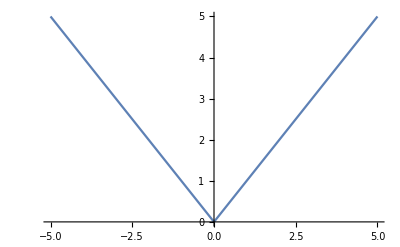

```mathematica
Plot[abs[x],{x,-5,5}]
```

```mathematica
abs2[x_]:=Piecewise[{{x,x>0},{-x,x<0}}]
```

```mathematica
Plot[abs2[x],{x,-5,5}]
```

-Graphics-

```mathematica
abs2[0]
```

0

```mathematica
(*Task1*)
task1[l_]:=(
For[i=1,i≤Length[l],i++,
If[l[[i]]≥0,Print[Sqrt[l[[i]]]],Print["The result is not a real number"]]
]
)
```

```mathematica
list5={1,-1,10,0,-4,13};
```

```mathematica
task1[list5]
```

1

The result is not a real number

√10

0

The result is not a real number

√13

```mathematica
(*Task2*)
d=0;
task2[x_,y_]:=({a,b}={x,y};
d=Mod[a,b];
If[a>b,
While[b!=0,
a=b;
b=d;
];
];
Print[a];
)
```

```mathematica
task2[30,5]
```

5

```mathematica
(*Task3*)
task3[x1_Real,y1_Real]:=(
Piecewise[{{Print["First"],x1>0.0 && y1>0.0},
{Print["Second"],x1<0.0 && y1>0.0},
{Print["Third"],x1<0.0 &&y1<0.0},
{Print["Fourth"],x1>0.0 && y1<0.0},
{Print["Abscissa"],x1==0&&y1≠0},
{Print["Ordinate"],x1≠0&&y1==0}}]
)
```

```mathematica
task3[2.3,1.4]
```

First

```mathematica
task3[2.3,-5.6]
```

Fourth

```mathematica
task3[0.0,2.4]
```

Abscissa

```mathematica
task3[2.4,0.0]
```

Ordinate

```mathematica
(*Tsk2.1*)
task21[a_,0]:=a;
task21[a_,b_]:=(task21[b,Mod[a,b]]);
```

```mathematica
task21[30,5]
```

5

```mathematica
(*Task5*)
x=1;
n=10;
Do[x=x*k,{k,n}]
x
```

3628800

```mathematica
10!
```

```mathematica
3628800
```

```mathematica
Factorial[10]
```

3628800

```mathematica
(*Task4*)
matrixMultiplicatior[m1_,m2_]:=(
If[Length[Dimensions[m1]]== 1 || Length[Dimensions[m2]]==1 ,
 Return["Invalid input!"]];
If[Dimensions[m1][[2]]≠ Dimensions[m2][[1]],
Return["Matrices have incompatible dimensions!"],

product=Table[0,{i,Dimensions[m1][[1]]},{j,Dimensions[m2][[2]]}];
For[row=1,row≤Dimensions[m1][[1]],row++,
For[col=1,col≤Dimensions[m2][[2]],col++,
product[[row,col]]=Sum[m1[[row,k]]*m2[[k,col]],{k,Dimensions[m1][[2]]}];
];
];
];
product//MatrixForm
)
```

```mathematica
A=({{a, b}, {c, d}});
```

```mathematica
B=({{e, f}, {g, h}});
```

```mathematica
matrixMultiplicatior[A,B]
```

(a e+b g | a f+b h
c e+d g | c f+d h)